## Isothermal atmosphere

S = ln ρ 
θc = R_B/R_c (bondi to core radius)

```mathematica
Quit
```

```mathematica
DSolve[{r^2 S'[r] == - θc, S[n θc] ==0},S[r],r][[1]]
```

{S[r]→(-r+n θc)/(n r)}

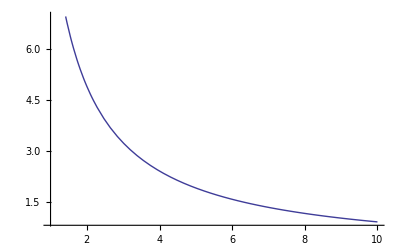

```mathematica
θc = 10;
n = 10;
Plot[(-r+n θc)/(n r),{r,1,θc}]
```

### Isothermal Mass

```mathematica
Assuming[θc>0,Integrate[4π r^2 Exp[θc/r],{r,1,θc}]]
```

2/3 π (-ⅇ^θc (2+θc+θc^2)+θc^3 (4 ⅇ-ExpIntegralEi[1]+ExpIntegralEi[θc]))

```mathematica
FullSimplify[%1]
```

2/3 π (-ⅇ^θc (2+θc+θc^2)+θc^3 (4 ⅇ-ExpIntegralEi[1]+ExpIntegralEi[θc]))

```mathematica
θc = 1/y;
Assuming[y>0,Series[2/3 π (-ⅇ^θc (2+θc+θc^2)+θc^3 (4 ⅇ-ExpIntegralEi[1]+ExpIntegralEi[θc])),{y,0,4}]] //Simplify
```

ⅇ^(1/y) (4 π y+O[y]^2)+((2 π (4 ⅇ-ExpIntegralEi[1]))/(3 y^3)+O[y]^5)

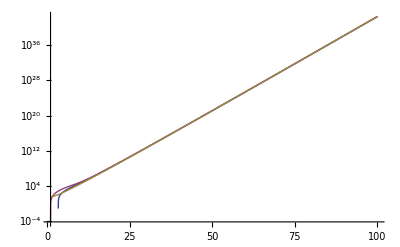

```mathematica
Clear[n]
LogPlot[{2/3 ⅇ^(-1/n) π (-ⅇ^θc (2+θc+θc^2)+θc^3 (ExpIntegralEi[θc])) /. n-> 10,2/3 ⅇ^(-1/n) π (-ⅇ^θc (2+θc+θc^2)+θc^3 (4 ⅇ-ExpIntegralEi[1]+ExpIntegralEi[θc])) /. n-> 20,4 π  (Exp[θc])/θc},{θc,1,100}]
```

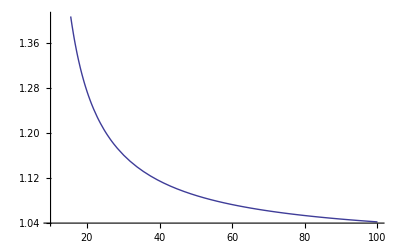

```mathematica
Plot[{2/3 ⅇ^(-1/n) π (-ⅇ^θc (2+θc+θc^2)+θc^3 (ExpIntegralEi[θc]))/(2/3 ⅇ^(-1/n) π 6 (Exp[θc])/θc) /. n-> 10},{θc,10,100}]
```

### Isothermal Critical Core Mass

Below plots approx value of θo for Matm = Mcore (isothermal)

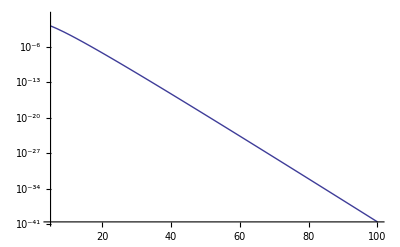

```mathematica
LogPlot[θc^2 Exp[-θc]/(4π),{θc,5,100}]
```

```mathematica
Assuming[x>0,Series[ExpIntegralEi[1/x],{x,0,4}]]//Simplify
```

ⅇ^(1/x) (x+x^2+2 x^3+6 x^4+O[x]^5)

```mathematica
Log[marr]/θcarr
```

{-0.104011,-0.0770429,-0.0513876,-0.0269513,-0.00364846,0.0185984,0.03986,0.0602008,0.0796798,0.098351,0.116264,0.133464,0.149994,0.165891,0.181193,0.195931,0.210137,0.22384,0.237065,0.249838}

```mathematica
Rc = 10^9;T = 60;ρ0 = 3*^-11;ρc = 2;
RG = (1.38*^-16)/(2.34 1.67*^-24);G = 6.67*^-8;
θ0 =(4 π  G ρ0 Rc^2)/(RG T)
θ1 = (4 π  G ρc Rc^2)/(3 RG T)
θc1 = 29.5;
Mc = √(3/(4 π ρc))((θc1 RG T)/G)^(3/2)
```

1.18675×10^-8

263.722

3.13424×10^26

```mathematica
1/(√(100ρ0))((RG T)/G)^(3/2)
```

1.03371×10^29

```mathematica
(G 25 6*^27)/(RG 270)
```

1.04932×10^12

```mathematica
((25 6*^27)/(3 2*^33))^(1/3)5 1.5*^13
```

2.19301×10^12

```mathematica
Mc/ME
```

0.0493292

```mathematica
θ0/θ1
```

4.5×10^-11

### ProductLog is a Bitch

```mathematica
Reduce[1 == ϵ Exp[x]/x,x]
```

C[1]∈Integers&&ϵ≠0&&x≠0&&x==-ProductLog[C[1],-ϵ]

```mathematica
-ProductLog[-1,-4.5 10^-12.]
```

29.5117

```mathematica
Assuming[ϵ>0,FullSimplify[Re[Series[-ProductLog[-1,-ϵ],{ϵ,0,1}]]]]
```

Re[(ⅈ π-Log[ϵ]+((-1+π+ⅈ Log[ϵ]) (-ⅈ+π+ⅈ Log[ϵ]) (1+π+ⅈ Log[ϵ]) Log[-ⅈ π+Log[ϵ]])/(π+ⅈ Log[ϵ])^3+((-3 ⅈ+π+ⅈ Log[ϵ]) Log[-ⅈ π+Log[ϵ]]^2)/(2 (π+ⅈ Log[ϵ])^3)+(ⅈ Log[-ⅈ π+Log[ϵ]]^3)/(3 (π+ⅈ Log[ϵ])^3))+O[ϵ]^2]

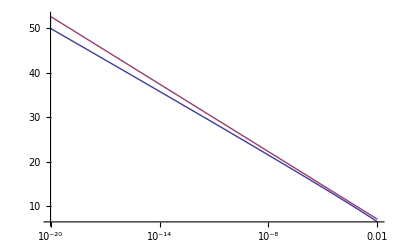

```mathematica
LogLinearPlot[{-ProductLog[-1,-ϵ],1.1(-Log[ϵ])+2},{ϵ,1*^-20,1*^-2}]
```

```mathematica
-ProductLog[-1,-E^-20.]+ProductLog[-1,-E^-10.]
```

10.6137

```mathematica
Exp[-20.]
```

2.06115×10^-9

```mathematica
%/10
```

1.06137

```mathematica
-ProductLog[-1,-E^-10.] - %106*10
```

1.91429

```mathematica
NSolve[1 == 4.5*^-12 Exp[x]/x,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→4.5×10^-12},{x→29.5117}}

## Adiabatic Atmosphere

### mass w Helium included

```mathematica
Quit
```

```mathematica
Δ = 0.3008849557522124;
γ = 1.4303797468354431;
```

```mathematica
Φ = Assuming[1>ϵ>0,Integrate[z^2(1 + Δ(1/z-1/ϵ))^(1/(γ-1)),{z,0,ϵ}]]
```

0.+0.0907401 ϵ^0.676471 Hypergeometric2F1[-2.32353,0.676471,1.67647,1.-3.32353 ϵ]

```mathematica
ser =  Assuming[1>ϵ>0,Series[Φ,{ϵ,0,0}]]
```

0.+(-1. (0.-3.32353 ϵ))^3.32353 ϵ^0.676471 (-0.0184692-0.0567897 ϵ+O[ϵ]^2)+ϵ^0.676471 (0.0376108+0.0845592 ϵ+O[ϵ]^2)

```mathematica
int /.
```

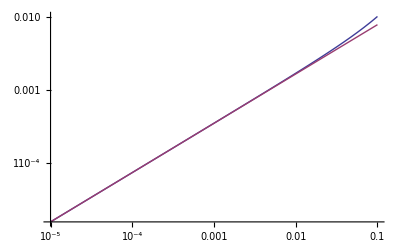

```mathematica
LogLogPlot[{Φ,0.03761 ϵ^0.6765 },{ϵ,1*^-5,1*^-1}]
```

```mathematica
4π 0.03761
```

0.472621

### mass in adiabatic region

```mathematica
M = 4 π ρcb RBp^3 Φ;
```

In dimensionless integral ϵ is ratio of R_CB/R_B’

```mathematica
Φ = Assuming[1>ϵ>0,Integrate[z^2(1 + 1/z-1/ϵ)^(5/2),{z,0,ϵ}]]
```

(15 √(-(-1+ϵ) ϵ)+10 √(-(-1+ϵ) ϵ^3)+8 √(-(-1+ϵ) ϵ^5)+15 ArcCos[√ϵ])/(24 √(-1+1/ϵ))

```mathematica
ser =  Assuming[1>ϵ>0,Series[Φ,{ϵ,0,2}]]
```

(5 π √ϵ)/16+5/32 π ϵ^(3/2)+O[ϵ]^(5/2)

```mathematica
Quit
```

```mathematica
Δ = 2/7;γ = 7/5;
Φ = Assuming[1>ϵ>0,Integrate[z^2(1 + Δ(1/z-1/ϵ))^(1/(γ-1)),{z,0,ϵ}]]
```

1/294 (15 ϵ+35 ϵ^2+98 ϵ^3+(30 ArcSinh[√(-1+(7 ϵ)/2)])/(√(49-14/ϵ)))

```mathematica
ser =  Assuming[1>ϵ>0,Series[Φ,{ϵ,0,2}]]
```

(5 π √ϵ)/(98 √14)+(5 π ϵ^(3/2))/(56 √14)+O[ϵ]^(5/2)

```mathematica
N[4 π(5 π √ϵ)/(98 √14)]/1.9^2.5
```

0.108182 √ϵ

This shows the result

```mathematica
Mat = 0.108 ρcb RB^(5/2)√rcb
```

```mathematica
1/(0.108/1.9)
```

17.5926

Check that new answer agrees with old answer that assumed a specific χ.  Yes!

```mathematica
5 π^2/4(Δ/χ)^(5/2)
```

0.106363

```mathematica
χ
```

1.91293

### Energy in adiabatic region

E = -cE  Pcb (RB')^3(RB'/Rc)^αE
diatomic
cE = 0.3133 , αE = 1/2
X = 0.7
cE = .717 , αE = 0.3235


E = -4 π Pcb (RB')^3Δ Φ2
provided that γ < 3/2 which is only marginally satisfied!

```mathematica
Φ2 = Assuming[{ϵ>0,γ>1},Integrate[z(Δad/z)^(1/(γ-1)),{z,ϵ,∞}]]
```

ConditionalExpression[-((-1+γ) Δad^(1/(-1+γ)) ϵ^(2+1/(1-γ)))/(-3+2 γ),γ<3/2]

```mathematica
4 π Δ Φ2 /. Δad -> Δ
```

0.717373/ϵ^0.323529

```mathematica
Φ2 = Assuming[ϵ>0,Integrate[z(Δ/z)^(1/(γ-1)),{z,ϵ,∞}]]
```

```mathematica
(8 √(2/7))/(49 √ϵ)//N
```

0.087269/(√ϵ)

```mathematica
Φ2 = Assuming[1>ϵ>0,Integrate[z(1+Δ/z)^(1/(γ-1)),{z,ϵ,1}]]
```

1/(98 √7)(288+16 √(7+2/ϵ)-63 √(ϵ (2+7 ϵ))-49 √(ϵ^3 (2+7 ϵ))+30 √7 ArcCsch[√(2/7)]-30 √7 ArcCsch[(√(2/7))/(√ϵ)])

```mathematica
Series[Φ2,{ϵ,0,0}]
```

(8 √(2/7))/(49 √ϵ)+(144/(49 √7)+15/49 ArcCsch[√(2/7)])+√O[ϵ]

```mathematica
Quit
```

```mathematica
γ
```

1.43038

```mathematica
γ = 7/5;Δ=2/7;
```

```mathematica
2+1/(1-γ)
```

-1/2

```mathematica
γ/(γ-1)
```

7/2

```mathematica
N[-((-1+γ) Δ^(1/(-1+γ)) ϵ^(2+1/(1-γ)))/(-3+2 γ)4 π Δ]
```

0.31333/(√ϵ)

```mathematica
N[-((-1+γ) Δ^(1/(-1+γ)) ϵ^(2+1/(1-γ)))/(-3+2 γ)4 π Δ]
```

0.717373/ϵ^0.323529

### Others

```mathematica
Quit
```

```mathematica
DSolve[ρ[r]^(γ-2)ρ'[r] r^2 == -θa,ρ[r],r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ[r]→((1-γ) (-θa/r-C[1]))^(1/(-1+γ))}}

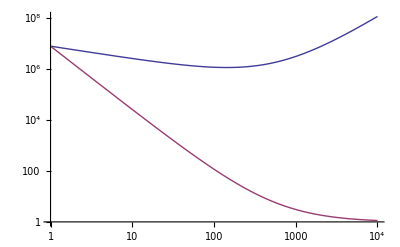

```mathematica
Δ = 2/7;γ = 1/(1-Δ);
θc = 2000;
LogLogPlot[{x^2(1+ (Δ θc)/x)^(1/(γ-1))-1,(1+ (Δ θc)/x-Δ/50)^(1/(γ-1))},{x,1,5 θc},PlotRange->Automatic]
```

```mathematica
(3γ-4)/(γ-1)
```

1/2

```mathematica
Δ^(1/(γ-1))
```

```mathematica
(2./7)^(5/2)
```

0.0436345

```mathematica
N[%]
```

0.285714^2.5

```mathematica
Quit
```

```mathematica
Δ = 2/7;γ = 1/(1-Δ);
```

```mathematica
N[4π Δ^(1/Δ)/1.9^(1/(γ-1))(γ-1)/(3-2γ)]
```

0.0629677

```mathematica
int = Assuming[l>0,Integrate[x^2(1 + 2/(7l)(1/x-1))^(5/2),{x,0,1}]]
```

1/3+5/(98 l^2)+5/(42 l)+(5 ArcSinh[√(-1+(7 l)/2)])/(49 √7 l^(5/2) √(-2+7 l))

```mathematica
Assuming[l>0,Series[4. π int,{l,0,1}]]
```

0.538319/l^(5/2)+0.942058/l^(3/2)+2.4729/(√l)+7.21263 √l-12.5664 l+O[l]^(3/2)

```mathematica
8π (2/7)^(5/2)//N
```

1.09665

```mathematica
(.54)/1.9^(5/2)
```

0.10852

```mathematica
(5 √(2/7) π^2)/(49 l^(5/2))//N
```

0.538319/l^(5/2)

```mathematica
(.063)/(3 1.9^4)
```

0.00161141

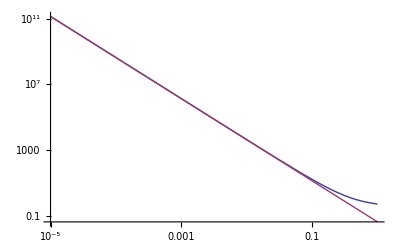

```mathematica
LogLogPlot[{int,(5 π)/(98 √14 l^(5/2))} ,{l,10^-5,1}]
```

```mathematica
int = Assuming[θc > 10,Integrate[3 x^2((1+Δ/x)^(1/(γ-1))),{x,1/θc,1}]]
```

1/(686 √7 θc^(5/2))(-7 (98 √(2+7/θc)+91 √(θc (7+2 θc))+33 √(θc^3 (7+2 θc)))+6 θc^(5/2) (777+5 √7 ArcSinh[√(7/2)])-30 √7 θc^(5/2) ArcSinh[(√(7/2))/(√θc)])

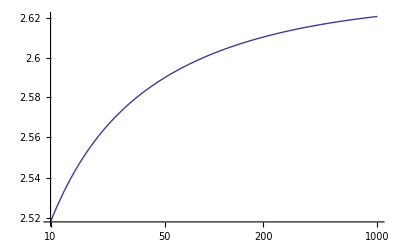

```mathematica
LogLogPlot[int,{θc,10,1000}]
```

## Critical mass adiabat

```mathematica
RH = (mc ME/(3 Mst))^(1/3)rr/10^5
```

1.4975×10^6 (mc/Ms)^(1/3) r

```mathematica
RG = kB/(2.34 mH);Δ = 2/7;κ0 = 0.1 κs;ρs = 2;
RB = (G mc ME)/(RG T);Rc = ((3 mc ME)/(4 π ρs))^(1/3)
Po = ρg RG T;
Lo = (64 π G mc ME σ T^4 Δ)/(3 κ0 Po) 
PM = (1.9 G mc ME^2)/RB^4
tcool = PowerExpand[0.55 (1.9 ξ PM)^3/Po^2 RB^(7/2)/(Lo √Rc)/yr /. r-> 5 r5]
Solve[tcool == 3 10^6,mc]//PowerExpand
```

8.93207×10^8 mc^(1/3)

(7.89288×10^25 fT^(7/2) mc r^(3/2))/(F √Ms κs)

(57934.8 fT^4)/(mc^3 r^(12/7))

(1.53637×10^14 fT^4 r5^(9/7) κs ξ^3)/(F mc^(20/3) √Ms)

{{mc→(14.3353 fT^(3/5) r5^(27/140) κs^(3/20) ξ^(9/20))/(F^(3/20) Ms^(3/40))}}

```mathematica
27./140
```

0.192857

```mathematica
(280./(T r^(1/2)))^(3/5)/. r-> 5.
```

1.55178 (1/fT)^(3/5)

```mathematica
T
```

(120 fT)/r^(3/7)

```mathematica
10^(.2)
```

1.58489

```mathematica
{PM /Po/. mc->(14.330012073644122 fT^(3/5) r5^(27/140) κs^(3/20) ξ^(9/20))/(F^(3/20) Ms^(3/40))/. r-> 5 r5}
```

{(19.3795 fT^(17/10) r5^(129/140))/(F^(11/20) Ms^(11/40) κs^(9/20) ξ^(27/20))}

```mathematica
Solve[x/(19.4 √Log[x])==1,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.00267},{x→36.843}}

```mathematica
36.8/19.4
```

1.89691

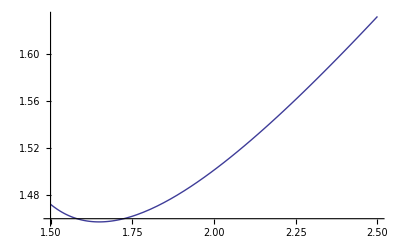

```mathematica
Plot[x/(1.6 √Log[x]),{x,1.5,2.5}]
```

```mathematica
27./140
```

0.192857

### Critical Core mass of Fully adaibatic atmosohere

Crude approximation neglecting compression entirely:

```mathematica
Mmax = √(3/(4 π ρg))((RG T)/G)^(3/2)/ME//PowerExpand
```

(25.3158 fT^(7/4) r^(3/4))/(√F Ms^(1/4))

## Pressure Radius Relation at Convective Boundary

Moved to RadiativeConvectiveBoundary.nb

## Solve For Core Mass

```mathematica
Quit
```

```mathematica
G=6.67*^-8;mH = 1.67*^-24;
σ = 5.67*^-5;kB = 1.38*^-16;
ME = 5.97*^27;RE = 6.38*^8;
Mst = 2.*^33 Ms;Rs = 6.96*^10;
Ω = 1.988*^-7 √Ms r^(-3/2);
AU = 1.5*^13;vK = Ω AU r;yr = 3.16*^7;rr = r AU;
```

```mathematica
μm = 2.35; (*marginal inconsistency if this isn't 2, but γ = 7/5*)
cV = 5/2;
cP = cV + 1;
γ = cP/cV
Δ = 1/cP
μ = μm mH;RG = kB/μ;
```

7/5

2/7

### Disk Model

```mathematica
Σg := 2200.F r^(-3/2);
T = 120 fT r^(-3/7);
cg = PowerExpand[√(kB T/μ)];
Hg = cg/Ω;
Σp = 33 F Z  r^(-3/2);
ρo = Σg/Hg/√(2 π) ;(*λ =μ/(√2 ρg σmol);ν = cad λ/2;*)
Po = ρo cg^2;

tdisk = 3*^6 τc yr;
```

### Atmosphere Model

```mathematica
Clear[r, mc]
```

```mathematica
r = 5 r5;
```

```mathematica
r = 10 r10;
mc = 10 mnorm;
```

```mathematica
κs = 0.01;
```

```mathematica
κ100 = 2 κs;β = 2;ρc = 3; Mc = mc ME;
χ = Piecewise[{{1.91293, β ==2}, {1.52753, β ==1}}];
θ = Piecewise[{{0.556069, β ==2}, {0.285824, β ==1}}];
RH = ( Mc/(3 Mst))^(1/3)rr;
RB = (G Mc)/(RG T);RBp = Δ RB/χ;
Rc = ((3  Mc)/(4 π ρc))^(1/3);
Lo = (64 π G Mc σ T^4 Δ)/(3 κ100 (T/100)^β Po) χ^(4-β);
PM = (4 Δ^(3/2))/(5 π^2 √χ)(G Mc^2)/RBp^4;
(*ξg = 3.38*)
ratio = (PM/(θ Po))[[1]] (*give just numerical part!*);
ξg = Quiet[NSolve[xi == √Log[xi ratio],xi][[2,1,2]]]
tcapp = PowerExpand[4π (ξg  PM)^2/Po RBp^(7/2)/(Lo √Rc)/yr ]
PowerExpand[Solve[tcapp yr == tdisk, mnorm]]
(*L = Lo Po/Pcb;
En = 0.31 Pcb RBp^(7/2)/√Rc;
tcool = PowerExpand[4π (Pcb)^2/Po RBp^(7/2)/(Lo √Rc) ];
Prcb = Solve[tcool == tdisk,Pcb][[-1,1,2]];*)
```

3.55311

(1.5245×10^11 fT^(5/2) κs)/(mc^(5/3) r^(15/14))

{{}}

```mathematica
N[T]
```

(44.7311 fT)/r10^(3/7)

```mathematica
.714 130
```

92.82

```mathematica
Clear[Pcb, tcool]
```

#### check notes value of Prcb/Po. Works

```mathematica
Prcb = Solve[tcool == tdisk,Pcb][[-1,1,2]]
```

(1318.8 fT^(11/4) √τc)/(mc^(7/6) r5^(33/28) √κs)

```mathematica
Prcb/Po
```

(20534.3 fT^(9/4) r5^(57/28) √τc)/(F mc^(7/6) √Ms √κs)

#### Continue

Check xi value for current normalizitation.  Low value is unphysical as it gives presure below disk presure.

```mathematica
PM/(θ Po);
ratio = (PM/(θ Po))[[1]] (*give just numerical part!*);
ξg = Quiet[NSolve[xi == √Log[xi ratio],xi][[2,1,2]]]
```

2.44312

```mathematica
ξ = ξr √Log[130.] 
mcrit = Solve[Prcb == ξ PM, mc][[-1,1,2]]/. κs -> κ
```

2.20625 ξr

(130.018 fT^(3/2) κ^(3/5) ξr^(6/5))/(r5^(9/14) τc^(3/5))

```mathematica
Prcb/(θ Po) /.{ mc-> 125 mcs, κs -> 1 κ}
```

(129.018 fT^(9/4) r5^(57/28) √τc)/(F mcs^(7/6) √Ms √κ)

```mathematica
Prcb/Po
```

(20050.3 fT^(9/4) r5^(57/28) √τc)/(F mc^(7/6) √Ms √κs)

```mathematica
Lo
```

(4.39463×10^26 fT^(3/2) mc r5^(33/14))/(F √Ms κs)

```mathematica
57/28.
```

2.03571

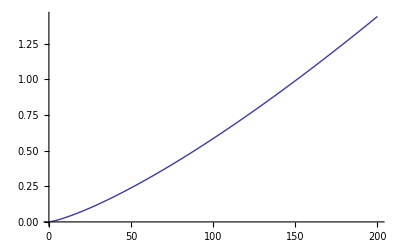

```mathematica
Plot[(0.004777 mc^(11/9))/(√Log[6310/mc^(7/9)]),{mc,1,200}]
```

```mathematica
Clear[Pcb]
```

```mathematica
Prcb
```

(1290.46 fT^(11/4) √τc)/(mc^(7/6) r5^(33/28) √κs)

## Solve For Core Mass Including Helium

Here the idea is γ ≠ 7/5, but should double check the RCB calculations (these values not in notes) plus Matm calculation.  This

```mathematica
Quit
```

```mathematica
G=6.67*^-8;mH = 1.67*^-24;
σ = 5.67*^-5;kB = 1.38*^-16;
ME = 5.97*^27;RE = 6.38*^8;
Mst = 2.*^33 Ms;Rs = 6.96*^10;
Ω = 1.988*^-7 √Ms r^(-3/2);
AU = 1.5*^13;vK = Ω AU r;yr = 3.16*^7;rr = r AU;
```

```mathematica
X = 0.7; Y = 1-X;mX = 2;mY = 4;
μm = (X/mX+Y/mY)^-1;
fX = μm X/mX;
cV = fX 5/2+ (1-fX)3/2;
cP = cV + 1;
γ = cP/cV
Δ = 1/cP
μ = μm mH;RG = kB/μ;
```

1.43038

0.300885

### Disk Model

```mathematica
Σg := 2200.F r^(-3/2);
T = 120 fT r^(-3/7);
cg = PowerExpand[√(kB T/μ)];
Hg = cg/Ω;
Σp = 33 F Z  r^(-3/2);
ρo = Σg/Hg/√(2 π) ;(*λ =μ/(√2 ρg σmol);ν = cad λ/2;*)
Po = ρo cg^2;

tdisk = 3*^6 τc yr;
```

### Atmosphere Model

```mathematica
Clear[r]
```

```mathematica
r = 5 r5;
```

```mathematica
κ100 = 2 κs;β = 1;ρc = 2; Mc = mc ME;
cm = 0.4726;αm = 0.6765;(*From numerical solution for atmosphere mass*)
cE = 0.717;αE = 0.3235;
Δo = 1/(4-β);
χ =(1-Δ/Δo)^((- 1)/(4-β));
θ = Piecewise[{{1.93, β ==2}, {5.50, β ==1}}](*Factor in pressure radius relation at RCB*)
RH = ( Mc/(3 Mst))^(1/3)rr;
RB = (G Mc)/(RG T);RBp = RB/χ;
Rc = ((3  Mc)/(4 π ρc))^(1/3);

PM = (G Mc^2)/(cm χ^αm RBp^4);
Lo = (64 π G Mc σ T^4 Δ)/(3 κ100 (T/100)^β Po) χ^(4-β);

(*tcool = PowerExpand[0.55 (2. ξ PM)^3/Po^2 RB^(7/2)/(Lo √Rc)/yr ]*)
L = Lo Po/Pcb;
En = cE Pcb RBp^3 (RBp/Rc)^αE;
tcool = PowerExpand[En/(2 L) ];
Prcb = Solve[tcool == tdisk,Pcb][[-1,1,2]];
```

5.5

```mathematica
Prcb/(Po)
```

(33864.1 fT^2.66175 r5^1.85925 √τc)/(F mc^1.10783 √Ms √κs)

```mathematica
ξ = ξr √Log[133000.] 
mcrit = Solve[Prcb == ξ PM, mc][[-1,1,2]]/. κs -> .01κ//PowerExpand
```

3.43484 ξr

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(10.7836 fT^0.939567 κ^0.560433401830749 ξr^1.1208668036615)/(r5^0.402671 τc^0.560433401830749)

```mathematica
θ Prcb/(Po) /.{ mc-> 10.8 mcs, κs -> .01 κ}
```

(133426. fT^2.66175 r5^1.85925 √τc)/(F mcs^1.10783 √Ms √κ)

```mathematica
Prcb/Po
```

(20050.3 fT^(9/4) r5^(57/28) √τc)/(F mc^(7/6) √Ms √κs)

```mathematica
Lo
```

(4.39463×10^26 fT^(3/2) mc r5^(33/14))/(F √Ms κs)

```mathematica
57/28.
```

2.03571

```mathematica
Plot[(0.004777 mc^(11/9))/(√Log[6310/mc^(7/9)]),{mc,1,200}]
```

-Graphics-

```mathematica
Clear[Pcb]
```

```mathematica
Prcb
```

(1290.46 fT^(11/4) √τc)/(mc^(7/6) r5^(33/28) √κs)

## Optical Depth Issue

```mathematica
T
```

(12 10^(4/7) fT)/r10^(3/7)

```mathematica
β = 2;
κ = κ100 (N[T]/100)^β
```

(0.400175 fT^2 κs)/r10^(6/7)

```mathematica
κ (PM RB^2)/(G Mc)
```

(74489.9 fT^4 κs)/(mnorm r10^(12/7))

```mathematica
(κ0 Po RB^2)/(G Mc)
```

(0.567003 F mc √Ms κs)/(fT^(3/2) r5^(33/14))

```mathematica
1.4/1.7
```

0.823529

## EOS

```mathematica
X = 0.7;Z = 0.0;Y = 1-X-Z;
mX = 2;mY = 4;mZ = 20;
μ = (X/mX+Y/mY+Z/mZ)^-1
fX = μ X/mX
cV = fX 5/2+ (1-fX)3/2
cP = cV + 1;
γ = cP/cV
Δ = 1/cP;
```

2.35294

0.823529

2.32353

1.43038

```mathematica
.10
```

```mathematica
2./7
```

0.285714

```mathematica
1/cP
```

0.300885

## H_2 dissociation

```mathematica
h = 6.63*^-27;
dEeV = 4.476;
dEinK = dEeV*(1.6*^-12)/kB
```

51895.7

```mathematica
(dEeV 1.6*^-12)/(Δ G Mc 2 mH/Rc) /. mc -> 10 m10
```

3.44388/m10^(2/3)

```mathematica
Δ G Mc 2 mH/Rc
```

4.48018×10^-13 mc^(2/3)

```mathematica
(1.6*^-12)/kB
```

```mathematica
ergoneV = h/4.1357*^-15
```

1.60311×10^-12

```mathematica
mH
```

1.67×10^-24

```mathematica
Tc = Δ (G Mc)/(RG Rc)
Pdiss = (π mH/h^2)^(3/2)(kB Tc)^(5/2)Exp[-dEinK/Tc]
TCB = χ 24 5^(4/7);TCB = 150.
PdissCB = (π mH/h^2)^(3/2)(kB TCB)^(5/2)Exp[-dEinK/TCB]
```

3819.42 mc^(2/3)

8.31667×10^12 ⅇ^(-13.5873/mc^(2/3)) mc^(5/3)

150.

1.41867×10^-141

```mathematica
Tex = 10^3.54
PdissCB = (π mH/h^2)^(3/2)(kB Tex)^(5/2)Exp[-dEinK/Tex]
```

3467.37

2.06504×10^6

```mathematica
Pdiss /. mc-> 10
```

2.06684×10^13

```mathematica
Po
```

(0.0641839 F √fT √Ms)/r5^(45/14)

```mathematica
γ
```

1.43038

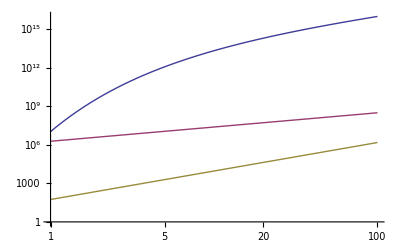

```mathematica
LogLogPlot[{Pdiss,2173.5/mc^1.1078(Tc/TCB)^(1/Δ),0.06418(Tc/TCB)^(1/Δ)},{mc,1,100}]
```

```mathematica
Prcb
```

(2173.53 fT^3.16175 √τc)/(mc^1.10783 r5^1.35504 √κs)

```mathematica
2/7.
```

0.285714